## Numerators

## Algebra utilities

```mathematica
SetDirectory[NotebookDirectory[]]
<<"./tools/tensTools.m"
<<"./tools/ampTools2.1.m"
```

/Users/zeno/Desktop/LTD/program/alphaLoopMisc

The documented functions in this package are: 
 ?extractTensCoeff
 ?getSymNumericCoeff

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

## Numerators

### Numerator definitions

#### Double Triangle

```mathematica
dtNum[k_,l_,p1_,p2_]:=(
(-I  gamma[s[11],mu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I  gamma[s[13],mu2,s[14]] T[a[11],i[11],i[12]])
I vector[l,mu3]gamma[s[14],mu3,s[15]]
(-I  gamma[s[15],nu,s[16]])
I vector[l-p1-p2,mu4]gamma[s[16],mu4,s[17]]
(-I  gamma[s[17],mu2,s[18]] T[a[11],i[12],i[11]])
I vector[k-p1-p2,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

dtNumerator[k_,l_,p1_,p2_]=contractColor[contractSpin[dtNum[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

512 SP[k,p1] SP[k,p2] SP[l,l]-512 SP[k,l] SP[k,p2] SP[l,p1]-256 SP[k,p1] SP[k,p2] SP[l,p1]+256 SP[k,p2]^2 SP[l,p1]+256 SP[k,p2] SP[l,p1]^2-512 SP[k,l] SP[k,p1] SP[l,p2]+256 SP[k,p1]^2 SP[l,p2]-256 SP[k,p1] SP[k,p2] SP[l,p2]+512 SP[k,k] SP[l,p1] SP[l,p2]-256 SP[k,p1] SP[l,p1] SP[l,p2]-256 SP[k,p2] SP[l,p1] SP[l,p2]+256 SP[k,p1] SP[l,p2]^2+256 SP[k,l] SP[k,p2] SP[p1,p1]-256 SP[k,p2] SP[l,l] SP[p1,p1]-256 SP[k,k] SP[l,p2] SP[p1,p1]+256 SP[k,l] SP[l,p2] SP[p1,p1]+512 SP[k,p2] SP[l,p2] SP[p1,p1]+512 SP[k,l]^2 SP[p1,p2]-256 SP[k,l] SP[k,p1] SP[p1,p2]-256 SP[k,l] SP[k,p2] SP[p1,p2]-256 SP[k,k] SP[l,l] SP[p1,p2]-256 SP[k,l] SP[l,p1] SP[p1,p2]+512 SP[k,p1] SP[l,p1] SP[p1,p2]-256 SP[k,l] SP[l,p2] SP[p1,p2]+512 SP[k,p2] SP[l,p2] SP[p1,p2]-256 SP[k,l] SP[p1,p1] SP[p1,p2]+256 SP[k,l] SP[k,p1] SP[p2,p2]-256 SP[k,p1] SP[l,l] SP[p2,p2]-256 SP[k,k] SP[l,p1] SP[p2,p2]+256 SP[k,l] SP[l,p1] SP[p2,p2]+512 SP[k,p1] SP[l,p1] SP[p2,p2]-512 SP[k,l] SP[p1,p1] SP[p2,p2]-256 SP[k,l] SP[p1,p2] SP[p2,p2]

#### 2 to2 (with initial quarks)

```mathematica
twoNum[k_,l_,p_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],nu,s[12]])
 I vector[k+q,mu1]gamma[s[12],mu1,s[13]]
(-I e gamma[s[13],mu,s[14]])
I vector[k+p,mu3]gamma[s[14],mu3,s[15]]
(-I gs gamma[s[15],mu2,s[16]])
I vector[k+l+p,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
)

twoNumerator[k_,l_,p_,q_,mu_,nu_]=contractSpin[twoNum[k,l,p,mu,nu,gs,e,q],{k,l,p,q}]/.{gs->1,e->1,d->4}
```

8 g[mu,nu] SP[k,k]^2+8 g[mu,nu] SP[k,k] SP[k,l]+16 g[mu,nu] SP[k,k] SP[k,p]+8 g[mu,nu] SP[k,k] SP[k,q]+16 g[mu,nu] SP[k,l] SP[k,q]+16 g[mu,nu] SP[k,p] SP[k,q]+8 g[mu,nu] SP[k,k] SP[l,p]+8 g[mu,nu] SP[k,q] SP[l,p]-8 g[mu,nu] SP[k,k] SP[l,q]-8 g[mu,nu] SP[k,p] SP[l,q]+8 g[mu,nu] SP[k,k] SP[p,p]+8 g[mu,nu] SP[k,q] SP[p,p]+8 g[mu,nu] SP[k,l] SP[p,q]-16 SP[k,k] vector[k,mu] vector[k,nu]-32 SP[k,l] vector[k,mu] vector[k,nu]-32 SP[k,p] vector[k,mu] vector[k,nu]-16 SP[l,p] vector[k,mu] vector[k,nu]-16 SP[p,p] vector[k,mu] vector[k,nu]+8 SP[k,k] vector[k,nu] vector[l,mu]+16 SP[k,p] vector[k,nu] vector[l,mu]+8 SP[p,q] vector[k,nu] vector[l,mu]+8 SP[k,k] vector[k,mu] vector[l,nu]-8 SP[p,q] vector[k,mu] vector[l,nu]-16 SP[k,l] vector[k,nu] vector[p,mu]-8 SP[l,q] vector[k,nu] vector[p,mu]+8 SP[k,k] vector[l,nu] vector[p,mu]+8 SP[k,q] vector[l,nu] vector[p,mu]+8 SP[l,q] vector[k,mu] vector[p,nu]-8 SP[k,k] vector[l,mu] vector[p,nu]-8 SP[k,q] vector[l,mu] vector[p,nu]-8 SP[k,k] vector[k,nu] vector[q,mu]-16 SP[k,l] vector[k,nu] vector[q,mu]-16 SP[k,p] vector[k,nu] vector[q,mu]-8 SP[l,p] vector[k,nu] vector[q,mu]-8 SP[p,p] vector[k,nu] vector[q,mu]+8 SP[k,k] vector[l,nu] vector[q,mu]+8 SP[k,p] vector[l,nu] vector[q,mu]-8 SP[k,l] vector[p,nu] vector[q,mu]-8 SP[k,k] vector[k,mu] vector[q,nu]-16 SP[k,l] vector[k,mu] vector[q,nu]-16 SP[k,p] vector[k,mu] vector[q,nu]-8 SP[l,p] vector[k,mu] vector[q,nu]-8 SP[p,p] vector[k,mu] vector[q,nu]+8 SP[k,k] vector[l,mu] vector[q,nu]+8 SP[k,p] vector[l,mu] vector[q,nu]-8 SP[k,l] vector[p,mu] vector[q,nu]

#### Bubble

```mathematica
bubNum[k_,l_,p1_,p2_,p_]:=(
(-I  gamma[s[11],nu,s[12]])
 I vector[k-p1-p2,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu,s[14]])
I vector[k,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],mu2,s[16]]T[a[11],i[11],i[12]])
I vector[l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]] T[a[11],i[12],i[11]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

bubNumerator[k_,l_,p1_,p2_,p_]=contractColor[contractSpin[bubNum[k,l,p1,p2,p],{k,l,p1,p2,p}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

-1024 SP[k,l] SP[k,p1] SP[k,p2]+256 SP[k,k] SP[k,p2] SP[l,p1]+256 SP[k,k] SP[k,p1] SP[l,p2]+512 SP[k,l] SP[k,p2] SP[p1,p1]-256 SP[k,k] SP[l,p2] SP[p1,p1]+512 SP[k,l] SP[k,p1] SP[p1,p2]+512 SP[k,l] SP[k,p2] SP[p1,p2]-256 SP[k,k] SP[l,p1] SP[p1,p2]-256 SP[k,k] SP[l,p2] SP[p1,p2]+512 SP[k,l] SP[k,p1] SP[p2,p2]-256 SP[k,k] SP[l,p1] SP[p2,p2]

#### 2 to 2 (with one initial gluon and one initial quark)

```mathematica
twoV2Num[k_,l_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],mu,s[12]])
 I vector[k+q,mu1]gamma[s[12],mu1,s[13]]
(-I gs gamma[s[13],mu2,s[14]])
I vector[l,mu3]gamma[s[14],mu3,s[15]]
(-I e gamma[s[15],nu,s[16]])
I vector[l+q,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
)

twoV2Numerator[k_,l_,q_,mu_,nu_]=contractSpin[twoV2Num[k,l,mu,nu,gs,e,q],{k,l,q}]/.{gs->1,e->1,d->4}
```

-8 g[mu,nu] SP[k,k] SP[l,l]-8 g[mu,nu] SP[k,q] SP[l,l]-8 g[mu,nu] SP[k,k] SP[l,q]-8 g[mu,nu] SP[k,l] SP[q,q]+16 SP[l,l] vector[k,mu] vector[k,nu]+16 SP[l,q] vector[k,mu] vector[k,nu]+8 SP[q,q] vector[k,nu] vector[l,mu]-32 SP[k,l] vector[k,mu] vector[l,nu]-16 SP[k,q] vector[k,mu] vector[l,nu]-16 SP[l,q] vector[k,mu] vector[l,nu]-8 SP[q,q] vector[k,mu] vector[l,nu]+16 SP[k,k] vector[l,mu] vector[l,nu]+16 SP[k,q] vector[l,mu] vector[l,nu]+8 SP[l,l] vector[k,nu] vector[q,mu]+8 SP[k,k] vector[l,nu] vector[q,mu]-16 SP[k,l] vector[l,nu] vector[q,mu]-16 SP[k,l] vector[k,mu] vector[q,nu]+8 SP[l,l] vector[k,mu] vector[q,nu]+8 SP[k,k] vector[l,mu] vector[q,nu]

#### 2 to2 s - channel

```mathematica
sChannelBubNum[k_,l_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],nu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I e gamma[s[13],mu,s[14]])
I vector[k+q,mu3]gamma[s[14],mu3,s[15]]
(-I gs gamma[s[15],mu2,s[16]])
I vector[k+q-l,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k+q,mu5]gamma[s[18],mu5,s[11]]
)

sChannelBubNumerator[k_,l_,q_,mu_,nu_]=contractSpin[sChannelBubNum[k,l,mu,nu,gs,e,q],{k,l,q}]/.{gs->1,e->1,d->4}
```

8 g[mu,nu] SP[k,k]^2-8 g[mu,nu] SP[k,k] SP[k,l]+24 g[mu,nu] SP[k,k] SP[k,q]+16 g[mu,nu] SP[k,q]^2-16 g[mu,nu] SP[k,k] SP[l,q]-16 g[mu,nu] SP[k,q] SP[l,q]+8 g[mu,nu] SP[k,k] SP[q,q]+8 g[mu,nu] SP[k,l] SP[q,q]+8 g[mu,nu] SP[k,q] SP[q,q]-16 SP[k,k] vector[k,mu] vector[k,nu]+32 SP[k,l] vector[k,mu] vector[k,nu]-32 SP[k,q] vector[k,mu] vector[k,nu]+32 SP[l,q] vector[k,mu] vector[k,nu]-16 SP[q,q] vector[k,mu] vector[k,nu]-8 SP[k,k] vector[k,nu] vector[l,mu]-16 SP[k,q] vector[k,nu] vector[l,mu]-8 SP[q,q] vector[k,nu] vector[l,mu]-8 SP[k,k] vector[k,mu] vector[l,nu]-16 SP[k,q] vector[k,mu] vector[l,nu]-8 SP[q,q] vector[k,mu] vector[l,nu]-8 SP[k,k] vector[k,nu] vector[q,mu]+16 SP[k,l] vector[k,nu] vector[q,mu]-16 SP[k,q] vector[k,nu] vector[q,mu]+16 SP[l,q] vector[k,nu] vector[q,mu]-8 SP[q,q] vector[k,nu] vector[q,mu]-8 SP[k,k] vector[k,mu] vector[q,nu]+16 SP[k,l] vector[k,mu] vector[q,nu]-16 SP[k,q] vector[k,mu] vector[q,nu]+16 SP[l,q] vector[k,mu] vector[q,nu]-8 SP[q,q] vector[k,mu] vector[q,nu]

#### 2 to 2 u - channel

```mathematica
uChannelNum[k_,l_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],mu,s[12]])
 I vector[k+q,mu1]gamma[s[12],mu1,s[13]]
(-I gs gamma[s[13],mu2,s[14]])
I vector[k+l+q,mu3]gamma[s[14],mu3,s[15]]
(-I e gamma[s[15],nu,s[16]])
I vector[k+l,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
)

uChannelNumerator[k_,l_,q_,mu_,nu_]=contractSpin[uChannelNum[k,l,mu,nu,gs,e,q],{k,l,q}]/.{gs->1,e->1,d->4}
```

-8 g[mu,nu] SP[k,k]^2-16 g[mu,nu] SP[k,k] SP[k,l]-16 g[mu,nu] SP[k,k] SP[k,q]-16 g[mu,nu] SP[k,l] SP[k,q]-16 g[mu,nu] SP[k,q]^2-8 g[mu,nu] SP[k,k] SP[l,l]-8 g[mu,nu] SP[k,q] SP[l,l]-8 g[mu,nu] SP[k,k] SP[l,q]-16 g[mu,nu] SP[k,q] SP[l,q]+8 g[mu,nu] SP[k,k] SP[q,q]+8 g[mu,nu] SP[k,l] SP[q,q]+16 SP[l,l] vector[k,mu] vector[k,nu]-16 SP[q,q] vector[k,mu] vector[k,nu]+16 SP[k,k] vector[k,nu] vector[l,mu]+16 SP[k,q] vector[k,nu] vector[l,mu]-8 SP[q,q] vector[k,nu] vector[l,mu]-16 SP[k,k] vector[k,mu] vector[l,nu]-32 SP[k,l] vector[k,mu] vector[l,nu]-16 SP[k,q] vector[k,mu] vector[l,nu]-16 SP[l,q] vector[k,mu] vector[l,nu]-8 SP[q,q] vector[k,mu] vector[l,nu]+16 SP[k,k] vector[l,mu] vector[l,nu]+16 SP[k,q] vector[l,mu] vector[l,nu]+16 SP[k,q] vector[k,nu] vector[q,mu]+8 SP[l,l] vector[k,nu] vector[q,mu]+16 SP[l,q] vector[k,nu] vector[q,mu]-8 SP[k,k] vector[l,nu] vector[q,mu]-16 SP[k,l] vector[l,nu] vector[q,mu]+16 SP[k,q] vector[k,mu] vector[q,nu]+8 SP[l,l] vector[k,mu] vector[q,nu]+8 SP[k,k] vector[l,mu] vector[q,nu]+16 SP[k,q] vector[l,mu] vector[q,nu]-16 SP[k,k] vector[q,mu] vector[q,nu]-16 SP[k,l] vector[q,mu] vector[q,nu]

### Scalar product, norm, tensor definitions

```mathematica
SP[k_,q_]:=k[[1]]q[[1]]-k[[2]]q[[2]]-k[[3]]q[[3]]-k[[4]]q[[4]]
norm[k_]:=Sqrt[k[[2]]^2+k[[3]]^2+k[[4]]^2]
vector[k_,mu_]:=k[[mu]]
g[mu_,nu_]:=-KroneckerDelta[mu,nu]+2 KroneckerDelta[mu,0]KroneckerDelta[nu,0]
```

### Tests

#### Double triangle, u - channel and st - channel equivalences

Numerators of cut diagrams obtained from the same vacuum bubble are the same up to re-routing

```mathematica
Simplify[dtNumerator[{k0,kx,ky,kz},-{l0,lx,ly,lz}-{q0,qx,qy,qz},-{q0,qx,qy,qz},1,1]-twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]]
```

-16 (k0^2-kx^2-ky^2-kz^2) l0^2+32 k0 l0 (k0 l0-kx lx-ky ly-kz lz)-16 k0^2 (l0^2-lx^2-ly^2-lz^2)-8 (k0^2-kx^2-ky^2-kz^2) (l0^2-lx^2-ly^2-lz^2)-16 (k0^2-kx^2-ky^2-kz^2) l0 q0+16 k0 (k0 l0-kx lx-ky ly-kz lz) q0+16 l0 (k0 l0-kx lx-ky ly-kz lz) q0-16 k0 (l0^2-lx^2-ly^2-lz^2) q0+16 k0 l0 (k0 q0-kx qx-ky qy-kz qz)-16 l0^2 (k0 q0-kx qx-ky qy-kz qz)-8 (l0^2-lx^2-ly^2-lz^2) (k0 q0-kx qx-ky qy-kz qz)-16 k0^2 (l0 q0-lx qx-ly qy-lz qz)-8 (k0^2-kx^2-ky^2-kz^2) (l0 q0-lx qx-ly qy-lz qz)+16 k0 l0 (l0 q0-lx qx-ly qy-lz qz)-8 (k0 l0-kx lx-ky ly-kz lz) (q0^2-qx^2-qy^2-qz^2)+dtNumerator[{k0,kx,ky,kz},{-l0-q0,-lx-qx,-ly-qy,-lz-qz},{-q0,-qx,-qy,-qz},1,1]

```mathematica
Simplify[dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]-uChannelNumerator[{k0,kx,ky,kz}-{q0,qx,qy,qz},{l0,lx,ly,lz}-{k0,kx,ky,kz},{q0,qx,qy,qz},1,1]]
```

-8 (-3 ky^2 l0^2-3 kz^2 l0^2+ky^2 lx^2+kz^2 lx^2+ky^2 ly^2+kz^2 ly^2+ky^2 lz^2+kz^2 lz^2+3 ky^2 l0 q0+3 kz^2 l0 q0-2 ky l0 ly q0-2 kz l0 lz q0+3 ky ly q0^2+3 kz lz q0^2-ky^2 lx qx-kz^2 lx qx-ky ly qx^2-kz lz qx^2+3 ky l0^2 qy-ky lx^2 qy-ky^2 ly qy-kz^2 ly qy-ky ly^2 qy-ky lz^2 qy-4 ky l0 q0 qy+2 ky lx qx qy+ky ly qy^2-kz lz qy^2+3 kz l0^2 qz-kz lx^2 qz-kz ly^2 qz-ky^2 lz qz-kz^2 lz qz-kz lz^2 qz-4 kz l0 q0 qz+2 kz lx qx qz+2 kz ly qy qz+2 ky lz qy qz-ky ly qz^2+kz lz qz^2+kx^2 (-3 l0^2+lx^2+ly^2+lz^2+3 l0 q0-lx qx-ly qy-lz qz)+k0 (4 kz l0 lz-l0^2 q0+3 lx^2 q0+3 ly^2 q0-2 kz lz q0+3 lz^2 q0+l0 q0^2-2 l0 lx qx-4 lx q0 qx+3 l0 qx^2+kx (4 l0 lx-2 lx q0-2 l0 qx)-2 l0 ly qy-4 ly q0 qy+3 l0 qy^2+ky (4 l0 ly-2 ly q0-2 l0 qy)-2 kz l0 qz-2 l0 lz qz-4 lz q0 qz+3 l0 qz^2)+k0^2 (l0^2-l0 q0-3 (lx^2+ly^2+lz^2-lx qx-ly qy-lz qz))-kx (-3 l0^2 qx+lx^2 qx+2 l0 q0 (lx+2 qx)+qx (ly^2+lz^2-2 ly qy-2 lz qz)+lx (-3 q0^2-qx^2+qy^2+qz^2)))+dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]

#### Bubble correction, s - channel and t - channel equivalences

Numerators of cut diagrams obtained from the same vacuum bubble are the same up to re - routing

```mathematica
Simplify[bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-sChannelBubNumerator[{k0,kx,ky,kz}-{q0,qx,qy,qz},-{l0,lx,ly,lz}+{k0,kx,ky,kz},{q0,qx,qy,qz},1,1]]
```

0

```mathematica
Simplify[bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz}-{k0,kx,ky,kz},{0,0,0,0},-{q0,qx,qy,qz},1,1]]
```

0

## Integrands

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Supergraph

```mathematica
dtSupergraph[k_,l_,p1_,p2_]:=(dtNumerator[k,l,p1,p2]/(SP[k,k]SP[l,l]SP[k-l,k-l]SP[l-p1-p2,l-p1-p2]SP[k-p1-p2,k-p1-p2]))

dtSupergraph[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}];
```

### Causal flow

```mathematica
phi[t_,k_,l_]:={t k, t l};

jacPhi[t_,k_,l_]:=t^6;
```

#### Flow solutions

```mathematica
vLsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
vRsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
rLsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]);
rRsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]);
```

#### Dirac delta jacobians

```mathematica
vLdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{ax,ay,az}] ,{ax,ay,az}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
vRdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
rLdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
rRdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Virtual contributions

#### Virtual left

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
dtVirtualLeft[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2k0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z},{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z}]))/.{p20->-p10+l0+norm[{0,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-l0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{k0->l0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{p20->-p10+l0+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{k0->p10+p20+norm[{0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{p20->-p10+l0+norm[{0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})

dtVirtualLeft[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-40.494

LU version (on - shell energy delta not yet solved)

```mathematica
dtVirtualLeftLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2k0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z},{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z}]))/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-l0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{k0->l0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{k0->p10+p20+norm[{0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})
```

#### Virtual Right

Toy model version (on-shell energy delta solved using q0)

-Graphics-

```mathematica
dtVirtualRight[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2l0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z},{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]))/.{p20->-p10+k0+norm[{0,kx,kx,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(k0-l0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->k0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(l0-p10-p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{l0->p10+p20+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtVirtualRightLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2l0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z},{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]))/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(k0-l0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{l0->k0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(l0-p10-p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{l0->p10+p20+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
```

### Real contributions

#### Real right

-Graphics-

Toy model version (on - shell energy delta solved using q0)

```mathematica
dtRealLeft[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(l0-k0)2(l0-p10-p20)]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{p20->-p10+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+l0}/.{l0->k0+norm[{0,lx-kx,ly-kx,lz-kz}]}/.{k0->norm[{0,kx,ky,kz}]}
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtRealLeftLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(l0-k0)2(l0-p10-p20)]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{l0 ->p20+p10-norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}
```

#### Real left

-Graphics-

Toy model version (on - shell energy delta solved using q0)

```mathematica
dtRealRight[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(-l0+k0)2(k0-p10-p20)]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]))/.{p20->-p10+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+k0}/.{k0->l0+norm[{0,lx-kx,ly-kx,lz-kz}]}/.{l0->norm[{0,lx,ly,lz}]}
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtRealRightLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(-l0+k0)2(k0-p10-p20)]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]))/.{k0 ->p20+p10-norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}
```

### Cross - section per supergraph

#### Toy model

```mathematica
dtSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=dtVirtualLeft[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtVirtualRight[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtRealLeft[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtRealRight[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

```mathematica
dtSum[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-54.8683

#### LU

```mathematica
dtLUrep[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vLt,vRt,rLt,rRt,sum,c},
vLt=vLsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
vRt=vRsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rLt=rLsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rRt=rRsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c=const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=( vLt^6(Exp[-vLt^2/sigma^2])/(vLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualLeftLU[vLt*kx,vLt*ky,vLt*kz,vLt*lx,vLt*ly,vLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+vRt^6(Exp[-vRt^2/sigma^2])/(vRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualRightLU[vRt*kx,vRt*ky,vRt*kz,vRt*lx,vRt*ly,vRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+
rLt^6(Exp[-rLt^2/sigma^2])/(rLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealLeftLU[rLt*kx,rLt*ky,rLt*kz,rLt*lx,rLt*ly,rLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rRt^6(Exp[-rRt^2/sigma^2])/(rRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealRightLU[rRt*kx,rRt*ky,rRt*kz,rRt*lx,rRt*ly,rRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

If[DEBUG,
Print["virtual Left: "];Print[c vLt^6(Exp[-vLt^2/sigma^2])/(vLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualLeftLU[vLt*kx,vLt*ky,vLt*kz,vLt*lx,vLt*ly,vLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["virtual Right: "];Print[c vRt^6(Exp[-vRt^2/sigma^2])/(vRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualRightLU[vRt*kx,vRt*ky,vRt*kz,vRt*lx,vRt*ly,vRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real Left: "];Print[c rLt^6(Exp[-rLt^2/sigma^2])/(rLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealLeftLU[rLt*kx,rLt*ky,rLt*kz,rLt*lx,rLt*ly,rLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real Right: "];Print[c rRt^6(Exp[-rRt^2/sigma^2])/(rRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealRightLU[rRt*kx,rRt*ky,rRt*kz,rRt*lx,rRt*ly,rRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];];

c*sum
];
```

```mathematica
dtLUrep[-0.02018173, 0.062112999,0.0898907771,-0.53934466291,-0.3918568348,0,1,0,0,1,1,0,0,-1,2,True]
```

virtual Left:

0.-37.8308 ⅈ

virtual Right:

0.+6.87465×10^-6 ⅈ

real Left:

0.+15.558 ⅈ

real Right:

0.+15.558 ⅈ

0.-6.71471 ⅈ

#### LU expression test

```mathematica
dtLUrep[-0.02018173, 0.062112999,0.0898907771,-0.53934466291,-0.3918568348,0,1,0,0,1,1,0,0,-1,2,True]
Print["-----------"]
Print["virtual Left benchmark: "];
Print["-37.86988"];
Print["virtual Right benchmark: "];
Print["0.00000687466"];
Print["real Left benchmark: "];
Print["15.5581"];
Print["real Right benchmark: "];Print["15.5581"];
```

virtual Left:

0.-37.8308 ⅈ

virtual Right:

0.+6.87465×10^-6 ⅈ

real Left:

0.+15.558 ⅈ

real Right:

0.+15.558 ⅈ

0.-6.71471 ⅈ

-----------

virtual Left benchmark:

-37.86988

virtual Right benchmark:

0.00000687466

real Left benchmark:

15.5581

real Right benchmark:

15.5581

### IR limits

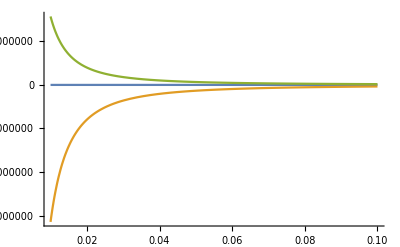

```mathematica
Plot[{dtSum[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1], dtVirtualRight[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1], dtRealRight[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1]},{eps,0.01,0.1},PlotRange->All]
```

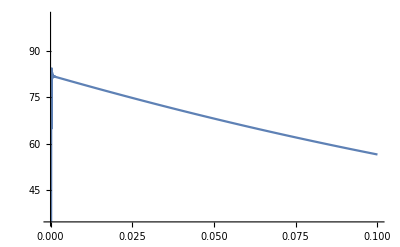

```mathematica
Plot[{dtSum[0.3,0.3,0.3,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1]},{eps,0.0,0.1}]
```

## -Graphics-

### Causal flow

```mathematica
eSurf1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]-norm[{0,lx,ly,lz}]-p10-p20;
eSurf2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}]-p10-p20;
```

```mathematica
lambda=0.01;
```

```mathematica
imPart[x1_,x2_,x3_,y1_,y2_,y3_]:=Dot[Grad[eSurf1[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1],{kx,ky,kz,lx,ly,lz}],{kx,ky,kz,lx,ly,lz}]/.{kx->x1,ky->x2,kz->x3,lx->y1,ly->y2,lz->y3}
```

```mathematica
FindInstance[imPart[kx,ky,kz,lx,ly,lz]>0 && eSurf1[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1]==0,{kx,ky,kz,lx,ly,lz},Reals]
```

$Aborted

```mathematica
Simplify[imPart[kx,ky,kz,lx,ly,lz]]
```

kx^2/(√(kx^2+ky^2+kz^2))+ky^2/(√(kx^2+ky^2+kz^2))+kz^2/(√(kx^2+ky^2+kz^2))+(kx (kx-lx))/(√((kx-lx)^2+(ky-ly)^2+(kz-lz)^2))+((kx-lx) lx)/(√((kx-lx)^2+(ky-ly)^2+(kz-lz)^2))+(ky (ky-ly))/(√((kx-lx)^2+(ky-ly)^2+(kz-lz)^2))+((ky-ly) ly)/(√((kx-lx)^2+(ky-ly)^2+(kz-lz)^2))+(kz (kz-lz))/(√((kx-lx)^2+(ky-ly)^2+(kz-lz)^2))+((kz-lz) lz)/(√((kx-lx)^2+(ky-ly)^2+(kz-lz)^2))+lx^2/(√(lx^2+ly^2+lz^2))+ly^2/(√(lx^2+ly^2+lz^2))+lz^2/(√(lx^2+ly^2+lz^2))

### Usual Cut

```mathematica
usualCut[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0+q0) 2(l0+k0)] SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{q0->-k0-norm[{k0,kx,ky,kz}+{q0,qx,qy,qz}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}] })
```

```mathematica
usualCut[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Weird Cut 1

This is the true and unique ISR singularity

-Graphics-

```mathematica
weirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=-((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[2l0 2(k0+q0) 4(k0)^3 ]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]))/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((1/Abs[2l0 2(k0+q0) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p0,0,0,0},{q0,qx,qy,qz},mu,nu]/(SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0}]),p0])/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{p0->0}
```

### Weird Cut 2

This one is a diagram without support, and should not be included ultimately.Indeed, there is no such singularity in the original diagram (once energy conservation is applied)

```mathematica
weirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[2(k0+l0) 2(k0+q0) 4(k0)^3 ]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{l0->-k0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}]}/.{k0->-norm[{0,kx,ky,kz}]})-
(((1/Abs[2norm[{0,kx,ky,kz}+{0,lx,ly,lz}] 2(k0+q0) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{p0,0,0,0},{q0,qx,qy,qz},mu,nu]/(SP[{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz}]),p0])/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{p0->0})
```

### Cross section per supergraph

```mathematica
twoSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=usualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+weirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+weirdCut2weirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]
```

### Ir limits

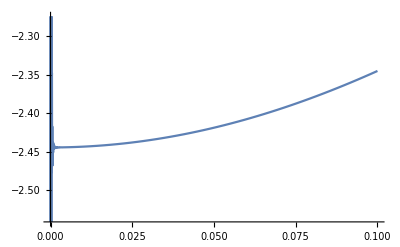

```mathematica
Plot[{weirdCut1[0,eps,0.5,0,0,1,0,0,0,1,1]+usualCut[0,eps,0.5,0,0,1,0,0,0,1,1]},{eps,0,0.1}]
```

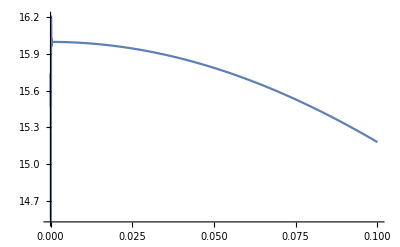

```mathematica
Plot[{weirdCut2[0,eps,-0.5,0,0,1,0,0,0,1,1]+usualCut[0,eps,-0.5,0,0,1,0,0,0,1,1]},{eps,0,0.1}]
```

## -Graphics-

### Usual cut

```mathematica
uChannelUsualCut[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0+l0)2(k0+q0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelUsualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

### Weird cut 1

```mathematica
uChannelWeirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2l0 2k0 2(k0+q0)]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelWeirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

### Weird Cut 2

```mathematica
uChannelWeirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0+l0)2(k0+l0+q0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{q0,qx,qy,qz}]))/.{q0->-l0-k0-norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,qx,qy,qz}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelWeirdCut2[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

### Cross section per supergraph

```mathematica
uChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=uChannelUsualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+uChannelWeirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+uChannelWeirdCut2[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]
```

### Ir limits

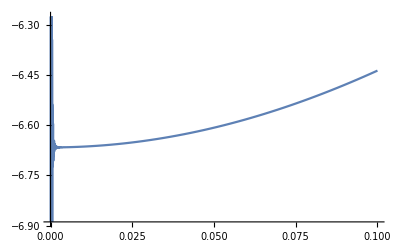

```mathematica
Plot[{uChannelWeirdCut1[0,eps,0.5,0,0,0.3,0,0,0,1,1]+uChannelUsualCut[0,eps,0.5,0,0,0.3,0,0,0,1,1]},{eps,0,0.1}]
```

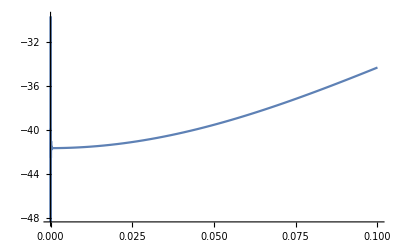

```mathematica
Plot[{uChannelWeirdCut2[0,eps,0.5,0,0,-0.3,0,0,0,1,1]+uChannelUsualCut[0,eps,0.5,0,0,-0.3,0,0,0,1,1]},{eps,0,0.1}]
```

## -Graphics-

### Only cut

This diagram has no singularities

```mathematica
sChannelBub[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((sChannelBubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2l0 2 (k0+q0-l0)2 k0] SP[{k0,kx,ky,kz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{q0,qx,qy,qz}]^2))/.{q0->l0-k0+norm[{0,kx,ky,kz}+{0,qx,qy,qz}-{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

sChannelBub[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Cross section per supergraph

```mathematica
sChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=sChannelBub[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]
```

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Causal flow

#### Flow Solutions

```mathematica
rSolBub[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
vSolBub[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
```

#### Dirac Delta Jacobians

```mathematica
rSolBubDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
vSolBubDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}],{sx,sy,sz}]/.{sx->kx,sy->ky,sz->kz};
```

### Real cut

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
bdReal[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0-l0)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->l0+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

LU version (on - shell energy delta not yet solved)

```mathematica
bdRealLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0-l0)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{k0->p10+p20-norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Virtual cut

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
bdVirtual[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(D[((bubNumerator[{k0,kx,ky,kz},{norm[{0,lx,ly,lz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2norm[{0,lx,ly,lz}]]SP[{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz},{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz}]))+(bubNumerator[{k0,kx,ky,kz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2 norm[{0,lx,ly,lz}-{0,kx,ky,kz}]]SP[{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz}]))),p0]/.{p0->0}/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
bdVirtual[kx,ky,kz,lx,ly,lz,1,0,0,1,0,0,-1];
```

LU version (on - shell energy delta not yet solved)

```mathematica
bdVirtualLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(D[((bubNumerator[{k0,kx,ky,kz},{norm[{0,lx,ly,lz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2norm[{0,lx,ly,lz}]]SP[{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz},{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz}]))+(bubNumerator[{k0,kx,ky,kz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2 norm[{0,lx,ly,lz}-{0,kx,ky,kz}]]SP[{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz}]))),p0]/.{p0->0}/.{k0->p10+p20-norm[{0,kx,ky,kz}]})
bdVirtualLU[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1];
```

### Cross section per supergraph

#### Toy model

```mathematica
bubbleSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=bdReal[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+bdVirtual[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z];
```

#### LU

```mathematica
bubLUrep[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,rt,sum,c},
rt=rSolBub[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
vt=vSolBub[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c=const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

Print[{vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz}];

sum=( vt^6(Exp[-vt^2/sigma^2])/(vSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdVirtualLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rt^6(Exp[-rt^2/sigma^2])/(rSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdRealLU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

If[DEBUG,
Print["virtual: "];
Print[c vt^6(Exp[-vt^2/sigma^2])/(vSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdVirtualLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];
Print[c rt^6(Exp[-rt^2/sigma^2])/(rSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdRealLU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];];

c*sum
];
```

#### LU expression test

```mathematica
bubLUrep[-0.0201817368890378,0.06211299937499417,0.08989077715277194,-0.5393446629166317,-0.39185683486164874,0,1,0,0,1,1,0,0,-1,2,True]
Print["-----------"]
Print["virtual benchmark: "];
Print["-0.0000294636"];
Print["real benchmark: "];
Print["4.001390989976316`"];
```

{-0.181636,0.559017,0.809017,-4.8541,-3.52671,0.}

virtual:

0.-0.0000294636 ⅈ

real:

0.+4.00139 ⅈ

0.+4.00136 ⅈ

-----------

virtual benchmark:

-0.0000294636

real benchmark:

4.001390989976316`

### Ir limits

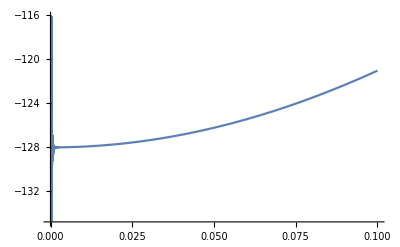

```mathematica
Plot[{bubbleSum[0,eps,1,0,0,0.5,1,0,0,1,0,0,-1](*,bdVirtual[0,eps,1,0,0,0.5,0,0,0,1,1], bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```

## -Graphics-

### Usual cut

```mathematica
v2UsualCut[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2k0 2(k0+l0+q0)2l0]SP[{k0,kx,ky,kz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{q0,qx,qy,qz}]SP[{l0,lx,ly,lz}+{q0,qx,qy,qz},{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{q0->-k0-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,qx,qy,qz}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->-norm[{0,kx,ky,kz}]})

v2UsualCut[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Weird cut 1

This one is a diagram without support, and should not be included ultimately. Indeed, there is no such singularity in the original diagram (once energy conservation is applied)

```mathematica
v2WeirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2k0 2(k0+q0)2(k0+l0+q0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}+{q0,qx,qy,qz},{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{l0->-k0-q0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,qx,qy,qz}]}/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->-norm[{0,kx,ky,kz}]})

v2WeirdCut1[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Weird cut 2

This is the true and unique ISR singularity

```mathematica
v2WeirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0+q0) 2 k0]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz}] SP[{l0,lx,ly,lz}+{q0,qx,qy,qz},{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{q0->-k0+norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

v2WeirdCut2[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Cross section per supergraph

```mathematica
stChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=v2UsualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+v2WeirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+v2WeirdCut2[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]
```

### Ir limits

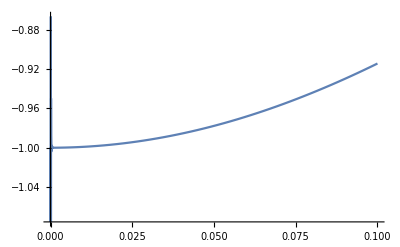

```mathematica
Plot[{v2UsualCut[0,eps,-0.5,0,0,1,0,0,0,1,1]+v2WeirdCut1[0,eps,-0.5,0,0,1,0,0,0,1,1](*, bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```

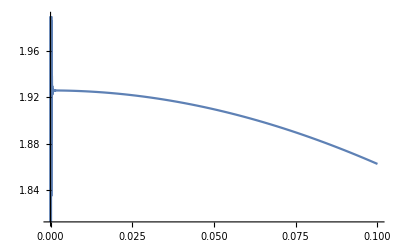

$Aborted

```mathematica
Plot[{v2UsualCut[0,eps,0.5,0,0,1,0,0,0,1,1]+v2WeirdCut2[0,eps,0.5,0,0,1,0,0,0,1,1](*, bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```